```mathematica
SetDirectory[NotebookDirectory[]];
$HistoryLength=0;
lenB=16;
countB=200;
typeB="Byte";
```

```mathematica
(*READ PLAINTEXT*)
plaintext={};
p=OpenRead["plaintext.bin",BinaryFormat->True];
For[i=1,i≤countB,i++,AppendTo[plaintext,N[BinaryReadList[p,typeB,lenB]]];];
Close[p];
Dimensions[plaintext](*dimensions of matrix of plaintexts*)
plaintext[[1,All]]//BaseForm[#,16]&
plaintext[[200,All]]//BaseForm[#,16]&
```

{200,16}

{(f8.)_16,(e9.)_16,(7a.)_16,(e5.)_16,80._16,(ed.)_16,(cd.)_16,(cd.)_16,45._16,13._16,(2d.)_16,36._16,(cb.)_16,(ef.)_16,(e5.)_16,24._16}

{85._16,21._16,(c7.)_16,(d8.)_16,7._16,17._16,(c6.)_16,(8a.)_16,(9a.)_16,(de.)_16,(8b.)_16,52._16,(5a.)_16,(5a.)_16,(2f.)_16,(d5.)_16}

```mathematica
(*READ CIPHERTEXT*)
ciphertext={};
c=OpenRead["ciphertext.bin",BinaryFormat->True];
For[i=1,i≤countB,i++,AppendTo[ciphertext,N[BinaryReadList[c,typeB,lenB]]];];
Close[c];
Dimensions[ciphertext](*dimensions of matrix of ciphertext*)
ciphertext[[1,All]]//BaseForm[#,16]&
ciphertext[[200,All]]//BaseForm[#,16]&
```

{200,16}

{(f9.)_16,(9f.)_16,30._16,(e8.)_16,63._16,(b1.)_16,(e9.)_16,(4d.)_16,(7e.)_16,62._16,(f.)_16,18._16,87._16,(8f.)_16,(f7.)_16,(fe.)_16}

{(e5.)_16,(c1.)_16,38._16,21._16,(3a.)_16,76._16,(4c.)_16,(aa.)_16,(1d.)_16,(fd.)_16,61._16,(a2.)_16,(7a.)_16,(b6.)_16,(7a.)_16,(1e.)_16}

```mathematica
(*READ TRACES*)
recLen=560001;
countT=200;
(*Define the amount we want to read from each trace*)
typeT="Integer16";
tracesAll={};
t=OpenRead["random-traces.bin",BinaryFormat->True];
For[i=1,i≤countT,i++,
AppendTo[tracesAll,N[BinaryReadList[t,typeT,recLen]]](*read whole trace*)
];
Close[t];
Dimensions[tracesAll]
(*dimensions of matrix of ciphertext*)
tracesAll[[3,All]]//BaseForm[#,16]&
tracesAll[[200,All]]//BaseForm[#,16]&
```

{200,560001}

{-5100._16,-5000._16,-5200._16,-5300._16,-5100._16,-5600._16,-5500._16,-5700._16,-5700._16,-4800._16,-5700._16,-5600._16,(-4a00.)_16,-2300._16,-1500._16,-1900._16,(-1b00.)_16,-2100._16,-2700._16,(-2d00.)_16,-3200._16,-3200._16,(-3a00.)_16,(-3b00.)_16,-4000._16,-4000._16,-4500._16,-4600._16,-4900._16,-4800._16,(-4e00.)_16,-5100._16,-5100._16,-5200._16,-6500._16,-5300._16,-5000._16,-3800._16,-2900._16,(-2b00.)_16,-3200._16,-3500._16,-3500._16,-4200._16,-4300._16,-4400._16,-4700._16,(-4b00.)_16,(-4f00.)_16,(-4d00.)_16,-5000._16,(-4f00.)_16,-5100._16,-5200._16,-5100._16,-5600._16,-5700._16,-5600._16,559886,-2800._16,(-2b00.)_16,-3200._16,-3800._16,(-3c00.)_16,(-3e00.)_16,-4300._16,-4600._16,-4700._16,(-4b00.)_16,(-4d00.)_16,(-4d00.)_16,-5200._16,-5300._16,-5500._16,(-5a00.)_16,-6000._16,-5400._16,-5600._16,-4200._16,-3400._16,-3800._16,(-3e00.)_16,(-3f00.)_16,(-4b00.)_16,(-4b00.)_16,(-4f00.)_16,(-4f00.)_16,-5200._16,-5400._16,-5500._16,-5800._16,-5800._16,-5900._16,-5900._16,(-5b00.)_16,(-5c00.)_16,(-5f00.)_16,(-5f00.)_16,-6000._16,(-5e00.)_16,-6000._16,-6100._16,(-5b00.)_16,-3300._16,(-1c00.)_16,-1000._16,-1300._16,-1800._16,-2300._16,(-2b00.)_16,(-2f00.)_16,-3300._16,-3400._16,(-3c00.)_16,(-3c00.)_16,-4200._16}
 |  |  |  |

{(-6a00.)_16,(-6b00.)_16,(-6c00.)_16,(-6d00.)_16,(-6d00.)_16,(-6f00.)_16,-7100._16,-7200._16,-6800._16,(-6a00.)_16,-7400._16,-7000._16,-5000._16,(-2f00.)_16,-3100._16,-3100._16,-3800._16,-3800._16,-4700._16,-4700._16,(-4c00.)_16,-5100._16,-5500._16,-5700._16,(-5b00.)_16,(-5e00.)_16,-6000._16,-6300._16,-6200._16,-6500._16,-6600._16,(-6b00.)_16,(-6c00.)_16,(-6f00.)_16,(-7e00.)_16,(-6a00.)_16,(-6c00.)_16,(-4d00.)_16,-4300._16,(-4c00.)_16,(-4c00.)_16,(-4d00.)_16,-5900._16,(-5b00.)_16,-6000._16,(-5f00.)_16,-6200._16,-6300._16,-6600._16,-6600._16,-6700._16,(-6c00.)_16,(-6b00.)_16,(-6c00.)_16,(-6e00.)_16,-7000._16,-7000._16,-7200._16,559886,(-3b00.)_16,-4100._16,-4500._16,(-4a00.)_16,(-4c00.)_16,-5200._16,-5500._16,-5800._16,(-5d00.)_16,(-5c00.)_16,-6200._16,-6000._16,-6600._16,-6800._16,(-6b00.)_16,(-6d00.)_16,-7600._16,-7700._16,(-6b00.)_16,-6200._16,(-4c00.)_16,(-4c00.)_16,-5300._16,-5300._16,-5800._16,-6000._16,-6100._16,-6400._16,-6200._16,-6800._16,-6900._16,(-6b00.)_16,(-6b00.)_16,(-6e00.)_16,(-6d00.)_16,(-6e00.)_16,(-6b00.)_16,-7000._16,-7300._16,-7300._16,-7600._16,(-6d00.)_16,-7500._16,-7700._16,(-5f00.)_16,(-4b00.)_16,(-2c00.)_16,-2300._16,-2900._16,(-2a00.)_16,(-3c00.)_16,(-3e00.)_16,-4600._16,-4700._16,(-4a00.)_16,-5200._16,-5300._16}
 |  |  |  |

```mathematica
ListLinePlot[{tracesAll[[1]]},PlotRange->All, PlotStyle->Orange]
ListLinePlot[{tracesAll[[2]]},PlotRange->All, PlotStyle->Orange]
ListLinePlot[{tracesAll[[11]]},PlotRange->All, PlotStyle->Orange]
ListLinePlot[{tracesAll[[200]]},PlotRange->All, PlotStyle->Orange]
```

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

```mathematica
start=15700;(*edit appropriately*)(*odskocit tu o neco ????*)
firstEnd = 80000;
lenDel=recLen-firstEnd;(*edit appropriately*)(*staci 1. runda*)
tracesStart=Drop[tracesAll,0,-lenDel];
traces=Drop[tracesStart,0,start];
Dimensions[traces]
```

{200,64300}

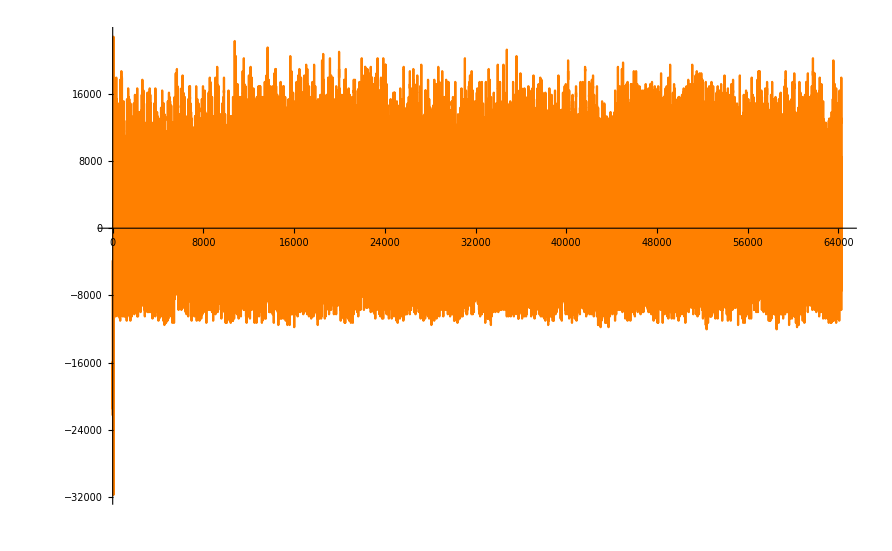

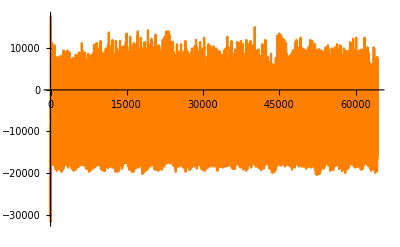

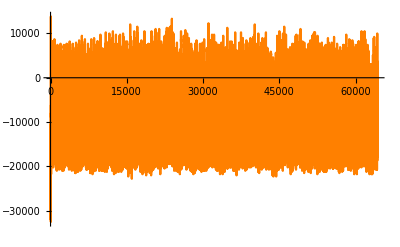

```mathematica
ListLinePlot[{traces[[2]]},PlotRange->All, PlotStyle->Orange]
ListLinePlot[{traces[[11]]},PlotRange->All, PlotStyle->Orange]
ListLinePlot[{traces[[200]]},PlotRange->All, PlotStyle->Orange]
```